## HOMOTOPY ANALYSIS METHOD (HAM) AT WORK

## TRIVIAL PROBLEM: L(u_0):-u_0+Wu_0+H=0; N(u):-u+Wu^2+H=0, ONE inhibitory population

```mathematica
(*choose parameters*)
w=-.1;
h=1;
(*I'm going to define W=ψw, H=ch and consider ψ in {ψmn,ψmx} and c in {cmn,cmx}*)
ψmx=2.;
cmx=1.9;
ψmn=.1;
cmn=.2;
ψst=.2;
cst=.2;

flagc0=0;(*c0 is the convergence parameter, this flag allows to implement it (flagc0=1) or not (flagc0=0)*)
```

```mathematica
ϕ[x_]:=x^2;
err1[u_,W_,H_]:=(-u+W ϕ[u]+H)^2;(*error function for calculating c0*)
Findc0[u_,W_,H_]:=With[{minsol=Minimize[err1[u,W,H],C0]},Part[Values@Last@minsol,1]];(*find c0 by minimizing the error function*)
res=Table[(*define the problem with the current values ψ and c*)
W=ψ w;
H=c h;
M=(1-W)^-1;
(*numerically find the solution for the nonlinear problem*)
sol=NSolve[u==W ϕ[u]+H,u,Reals][[2]];
(*find HAM approximate solution*)
u0=M H;(*HAM0 contributions*)
U0=u0;(*HAM0 solution*)
auxu1[c0_]:=c0 M(-u0+W u0^2+H);(*HAM1 contribution*)
auxU1[c0_]:=u0+auxu1[c0];(*HAM1 solution*)
If[flagc0>0,{c0=Findc0[auxU1[C0],W,H];u1=auxu1[c0];U1=auxU1[c0];},{u1=auxu1[1];U1=U0+u1;}];
auxu2[c0_]:=M((1-c0)u1-W u1+2c0 W(u0 u1));
auxU2[c0_]:=U1+auxu2[c0];
If[flagc0>0,{c0=Findc0[auxU2[C0],W,H];u2=auxu2[c0];U2=auxU2[c0];},{u2=auxu2[1];U2=U1+u2;}];
auxu3[c0_]:=M((1-c0)u2-W u2+c0 W u1^2+2c0 W (u0 u2));
auxU3[c0_]:=U2+auxu3[c0];
If[flagc0>0,{c0=Findc0[auxU3[C0],W,H];u3=auxu3[c0];U3=auxU3[c0];},{u3=auxu3[1],U3=U2+u3}];
auxu4[c0_]:=M((1-c0)u3-W u3+2c0 W u0 u3+2c0 W u1 u2);
auxU4[c0_]:=U3+auxu4[c0];
If[flagc0>0,{c0=Findc0[auxU4[C0],W,H];u4=auxu4[c0];U4=auxU4[c0];},{u4=auxu4[1],U4=U3+u4}];
{u/.sol,U0,U1,U2,U3,U4},(*this is what I write in res*)
{ψ,ψmn,ψmx,ψst},{c,cmn,cmx,cst}];
α=Table[c ψ,{ψ,ψmn,ψmx,ψst},{c,cmn,cmx,cst}];
dd1=Dimensions[α][[1]];
dd2=Dimensions[α][[2]];
ddm=Dimensions[res][[3]];
```

```mathematica
(*data structure for the plots*)
data:=Table[Table[{Flatten[Table[{α[[i,j]],res[[i,j,1]]},{i,1,dd1},{j,1,dd2}],1][[k]],Flatten[Table[{α[[i,j]],res[[i,j,m]]},{i,1,dd1},{j,1,dd2}],1][[k]]},{k,1,dd1 dd2}],{m,2,ddm}];
plotopts11={PlotStyle->Gray,Joined->True,PlotMarkers->{●,7},ImageSize->200};
(*compare the numerical solution with the HAMm (order m approximation) solution *)
PlotComparison1:=Row[Table[Show[{ListPlot[data[[m]],plotopts11,PlotLabel->StringJoin["HAM",ToString[m-1]],PlotRange->All,AxesLabel->{"α","e"}],ListPlot[data[[m,All,2]],PlotMarkers->{●,7},PlotStyle->ColorData[10]@m]}],{m,1,ddm-1}]]
```

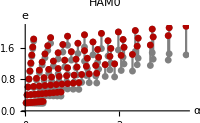
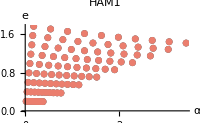
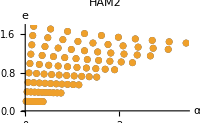
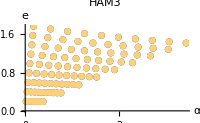
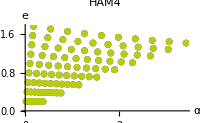

```mathematica
PlotComparison1
```

```mathematica
(*calculate the relative square error at perturbative order m*)
relsquareerr:=Table[((res[[i,j,m]]-res[[i,j,1]])/res[[i,j,1]])^2,{i,1,dd1},{j,1,dd2},{m,2,ddm}];
PlotSError:=Row[Table[ListPlot[Flatten[Table[{α[[i,j]],relsquareerr[[i,j,m]]},{i,1,dd1},{j,1,dd2}],1],PlotMarkers->{●,7},PlotStyle->ColorData[10]@m,ImageSize->200,AxesLabel->{"α","cumulative relative square error"},PlotLabel->StringJoin["HAM",ToString[m-1]],PlotRange->All],{m,1,ddm-1}]]
```

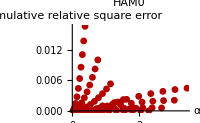
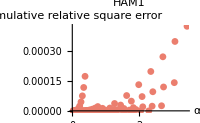
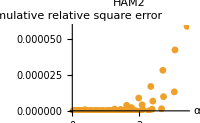
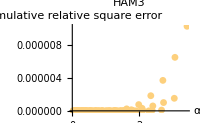
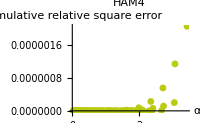

```mathematica
PlotSError
```

```mathematica
(*check the coonvergence of the HAM solution to the numerical solution when m increases*)
PlotConvergenceCheck1:=Row[{ListPlot[Flatten[Table[Abs[res[[i,j,2;;ddm]]-res[[i,j,1]]],{i,1,dd1},{j,1,dd2}],1],Joined->True,PlotStyle->ColorData["AvocadoColors"]/@(Range[1,dd1 dd2]/(dd1 dd2)),DataRange->{0,3},Frame->{{True,False},{True,False}},FrameLabel->{{"absolute error",None},{None,None}},FrameTicks->{{Automatic,None},{{{0,"HAM0"},{1,"HAM1"},{2,"HAM2"},{3,"HAM3"}},None}},ImageSize->Medium],BarLegend["AvocadoColors",LegendLabel->"α"]}]
```

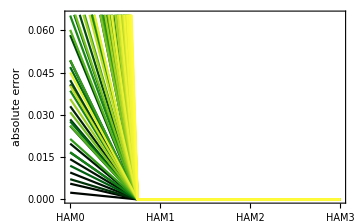

```mathematica
PlotConvergenceCheck1
```

## L(u_0):-u_0+Wu_0+h=0; N(u):-u+Wu^2+h=0, EP populations

LET US CONSIDER THE SYSTEM u={ue,up} with steady state equations u=Wu^2+H
Its full analytical solution can be found, but is unreadable

```mathematica
Solve[{ue==w1 ue^2-w2 up^2+h1,up==w3 ue^2-w4 up^2+h2},{ue,up}]
```

{{ue→-w4/(2 (w2 w3-w1 w4))-1/2 √(5+1)-1/2 √((2 w4^2)/(w2 w3-w1 w4)^2-(-w1 w2+2 h2 w2^2 w3-2 h2 w1 w2 w4-2 h1 w2 w3 w4+w4^2+2 h1 w1 w4^2)/(w2 w3-w1 w4)^2-1/(3 (1))-1/1-(1)^(1/3)/(3 2^(1/3) (1)^2)-(-(8 w4^3)/(w2 w3-w1 w4)^3-(8 (w2+2 h2 w2 w4-2 h1 w4^2))/(w2 w3-w1 w4)^2+(8 w4 (-w1 w2+2 h2 w2^2 w3-2 h2 w1 w2 w4-2 h1 w2 w3 w4+w4^2+2 h1 w1 w4^2))/(w2 w3-w1 w4)^3)/(4 √(w4^2/(w2 w3-w1 w4)^2-(-w1 w2+2 h2 w2^2 w3-2 h2 w1 w2 w4-2 h1 w2 w3 w4+w4^2+2 h1 w1 w4^2)/(w2 w3-w1 w4)^2+1/(3 (1))+(2^(1/3) (1))/(3 (1)^2 (1)^(1/3))+(1)^(1/3)/(3 2^(1/3) (w2 w3-w1 w4)^2)))),up→-1/w2},2,{ue→1,1}}
 |  |  |  |

We will solve the system numerically and compare the solution with the HAM approximation at order m (HAMm)

```mathematica
(*start from a given w and h of L2norm~1 and modify their norm*)
ψmx=1.9;
cmx=1;
ψmn=.1;
cmn=.2;
ψst=.2;
cst=.2;
w={{0.54,-0.26},{0.81,-0.11}};
h={0.91,0.42};
Norm[h]
Norm[w]
flagc0=1;
```

1.00225

1.00232

```mathematica
flagc0=1;
```

```mathematica
ϕ[x_]:=x^2;
err[{ue_,up_},W_,H_]:=Total@((-{ue,up}+W.ϕ[{ue,up}]+H)^2);
Findc0[u_,W_,H_]:=With[{minsol=Minimize[err[u,W,H],C0]},Part[Values@Last@minsol,1]];
res=Table[(*define the problem with the current values ψ and c*)
W=ψ w;
M=Inverse[IdentityMatrix[2]-W];
H=c h;
(*numerically find the solution for the nonlinear problem*)
u={ue,up};
sol=NSolve[u==W.ϕ[u]+H,u,Reals][[2]];
(*find HAM approximate solution*)
u0=M.H;(*HAM0 contributions*)
U0=u0;(*HAM0 solution for the total current*)
auxu1[c0_]:=c0 M.(-u0+W.u0^2+H);(*HAM1 contributions*)
auxU1[c0_]:=u0+auxu1[c0];
If[flagc0>0,{c0=Findc0[auxU1[C0],W,H];u1=auxu1[c0];U1=auxU1[c0];},{u1=auxu1[1];U1=U0+u1;}];
auxu2[c0_]:=M.((1-c0)u1-W.u1+2c0 W.(u0 u1));
auxU2[c0_]:=U1+auxu2[c0];
If[flagc0>0,{c0=Findc0[auxU2[C0],W,H];u2=auxu2[c0];U2=auxU2[c0];},{u2=auxu2[1];U2=U1+u2;}];
auxu3[c0_]:=M.((1-c0)u2-W.u2+c0 W.u1^2+2c0 W.(u0 u2));
auxU3[c0_]:=U2+auxu3[c0];
If[flagc0>0,{c0=Findc0[auxU3[C0],W,H];u3=auxu3[c0];U3=auxU3[c0];},{u3=auxu3[1],U3=U2+u3}];
auxu4[c0_]:=M.((1-c0)u3-W.u3+2c0 W.(u0 u3)+2c0 W.(u1 u2));
auxU4[c0_]:=U3+auxu4[c0];
If[flagc0>0,{c0=Findc0[auxU4[C0],W,H];u4=auxu4[c0];U4=auxU4[c0];},{u4=auxu4[1],U4=U3+u4}];
{u/.sol,U0,U1,U2,U3,U4},(*this is what I write in res*)
{ψ,ψmn,ψmx,ψst},{c,cmn,cmx,cst}];
α=Table[c ψ,{ψ,ψmn,ψmx,ψst},{c,cmn,cmx,cst}];
dd1=Dimensions[α][[1]];
dd2=Dimensions[α][[2]];
ddm=Dimensions[res][[3]];
```

```mathematica
(*data structure for the plots*)
datae:=Table[Table[{Flatten[Table[{α[[i,j]],res[[i,j,1,1]]},{i,1,dd1},{j,1,dd2}],1][[k]],Flatten[Table[{α[[i,j]],res[[i,j,m,1]]},{i,1,dd1},{j,1,dd2}],1][[k]]},{k,1,dd1 dd2}],{m,2,ddm}];
datap:=Table[Table[{Flatten[Table[{α[[i,j]],res[[i,j,1,2]]},{i,1,dd1},{j,1,dd2}],1][[k]],Flatten[Table[{α[[i,j]],res[[i,j,m,2]]},{i,1,dd1},{j,1,dd2}],1][[k]]},{k,1,dd1 dd2}],{m,2,ddm}];
plotopts1={PlotStyle->Gray,Joined->True,PlotMarkers->{●,7},ImageSize->200};
(*compare the numerical solution with the HAMm (order m-th approximation) solution *)
PlotComparison:={Row[Table[Show[{ListPlot[datae[[m]],plotopts1,PlotLabel->StringJoin["HAM",ToString[m-1]],PlotRange->All,AxesLabel->{"α","e"}],ListPlot[datae[[m,All,2]],PlotMarkers->{●,7},PlotStyle->ColorData[10]@m]}],{m,1,ddm-1}]],
Row[Table[Show[{ListPlot[datap[[m]],plotopts1,PlotLabel->StringJoin["HAM",ToString[m-1]],PlotRange->All,AxesLabel->{"α","p"}],ListPlot[datap[[m,All,2]],PlotMarkers->{●,7},PlotStyle->ColorData[10]@m]}],{m,1,ddm-1}]]};
cumrelsquareerr:=Table[Total[((res[[i,j,m,;;]]-res[[i,j,1,;;]])/res[[i,j,1,;;]])^2],{i,1,dd1},{j,1,dd2},{m,2,ddm}];
paradoxical:=Table[If[-W[[1,1]]+1/(2res[[i,j,m,1]])<0,2,1],{i,1,dd1},{j,1,dd2},{m,1,ddm}];
PlotParadoxical:={Row[Table[MatrixPlot[paradoxical[[All,All,m]]paradoxical[[All,All,1]],PlotTheme->"Minimal",ColorFunction->(ColorData["StarryNightColors"][Rescale[#,{0,4}]]&),ColorFunctionScaling->False,PlotLabel->If[m>1,StringJoin["HAM",ToString[m-2]],"full solution"]],{m,1,ddm}]],
SwatchLegend[ColorData["StarryNightColors"]/@{0.25,1,0.5},{"NON PARADOXICAL","PARADOXICAL","WRONG"}]};
(*calculate the relative square error at perturbative order m*)
PlotCSError:=Row[Table[ListPlot[Flatten[Table[{α[[i,j]],cumrelsquareerr[[i,j,m]]},{i,1,dd1},{j,1,dd2}],1],PlotMarkers->{●,7},PlotStyle->ColorData[10]@m,ImageSize->200,AxesLabel->{"α","cumulative relative square error"},PlotLabel->StringJoin["HAM",ToString[m-1]],PlotRange->All],{m,1,ddm-1}]];
(*check the coonvergence of the HAM solution to the numerical solution when m increases*)
PlotConvergenceCheck:=Row[{ListPlot[Flatten[Table[Abs[res[[i,j,2;;ddm,1]]-res[[i,j,1,1]]]+Abs[res[[i,j,2;;ddm,2]]-res[[i,j,1,2]]],{i,1,dd1},{j,1,dd2}],1],Joined->True,PlotStyle->ColorData["AvocadoColors"]/@(Range[1,dd1 dd2]/(dd1 dd2)),PlotRange->All,DataRange->{0,3},Frame->{{True,False},{True,False}},FrameLabel->{{"absolute error",None},{None,None}},FrameTicks->{{Automatic,None},{{{0,"HAM0"},{1,"HAM1"},{2,"HAM2"},{3,"HAM3"}},None}},ImageSize->Medium],BarLegend["AvocadoColors",LegendLabel->"α"]}]
```

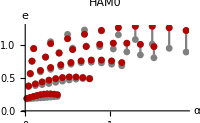
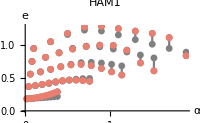
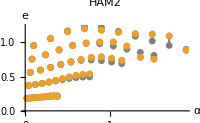
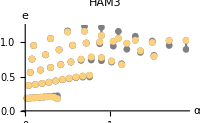
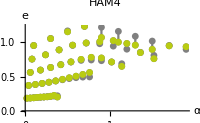
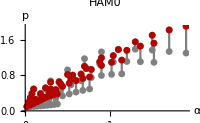
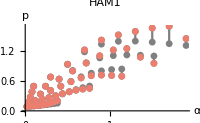
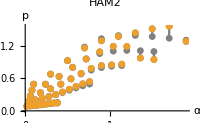

```mathematica
PlotComparison
```

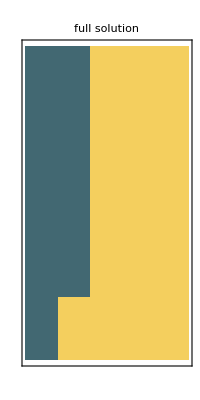
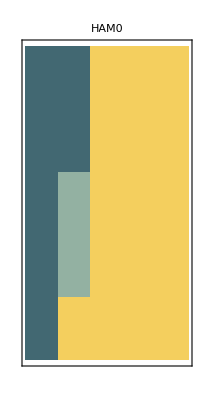
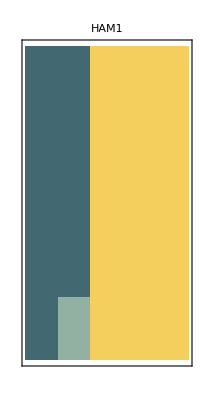
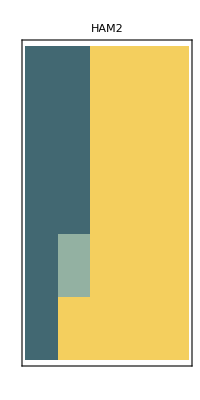
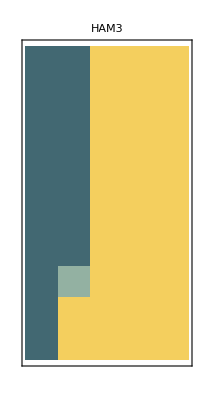
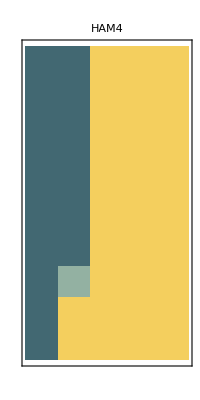

```mathematica
PlotParadoxical
```

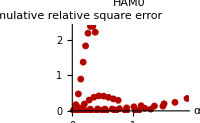
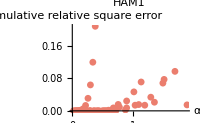
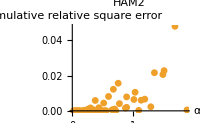
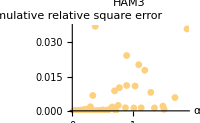
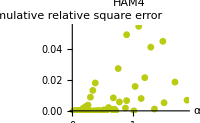

```mathematica
PlotCSError(*c0*)
```

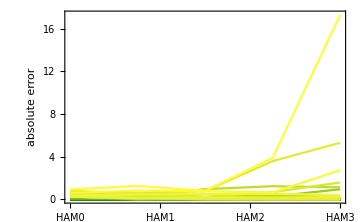

```mathematica
PlotConvergenceCheck
```

## L(u_0):-u_0+h=0; N(u):-u+Wu^2+h=0

```mathematica
flagc0=1;
ϕ[x_]:=x^2;
err[{ue_,up_},W_,H_]:=Total@((-{ue,up}+W.ϕ[{ue,up}]+H)^2);
Findc0[u_,W_,H_]:=With[{minsol=Minimize[err[u,W,H],C0]},Part[Values@Last@minsol,1]];
res=Table[(*define the problem with the current norms ψ and c*)
W=ψ w;
M=Inverse[IdentityMatrix[2]-W];
H=c h;
(*numerically find the solution for the nonlinear problem*)
u={ue,up};
sol=NSolve[u==W.ϕ[u]+H,u,Reals][[2]];
(*find HAM approximate solution*)
u0=H;(*HAM0 contributions*)
U0=u0;(*HAM0 solution*)
auxu1[c0_]:=c0 (W.u0^2-u0+h);(*HAM1 contributions*)
auxU1[c0_]:=u0+auxu1[c0];
If[flagc0>0,{c0=Findc0[auxU1[C0],W,H];u1=auxu1[c0];U1=auxU1[c0];},{u1=auxu1[1];U1=U0+u1;}];
auxu2[c0_]:=(1-c0)u1+2c0 W.(u0 u1);
auxU2[c0_]:=U1+auxu2[c0];
If[flagc0>0,{c0=Findc0[auxU2[C0],W,H];u2=auxu2[c0];U2=auxU2[c0];},{u2=auxu2[1];U2=U1+u2;}];
auxu3[c0_]:=(1-c0)u2+c0 W.u1^2+2c0 W.(u0 u2);
auxU3[c0_]:=U2+auxu3[c0];
If[flagc0>0,{c0=Findc0[auxU3[C0],W,H];u3=auxu3[c0];U3=auxU3[c0];},{u3=auxu3[1],U3=U2+u3}];
auxu4[c0_]:=(1-c0)u3+2c0 W.(u0 u3)+2c0 W.(u1 u2);
auxU4[c0_]:=U3+auxu4[c0];
If[flagc0>0,{c0=Findc0[auxU4[C0],W,H];u4=auxu4[c0];U4=auxU4[c0];},{u4=auxu4[1],U4=U3+u4}];
{u/.sol,U0,U1,U2,U3,U4},
{ψ,ψmn,ψmx,ψst},{c,cmn,cmx,cst}];
α=Table[c ψ,{ψ,ψmn,ψmx,ψst},{c,cmn,cmx,cst}];
dd1=Dimensions[α][[1]];
dd2=Dimensions[α][[2]];
ddm=Dimensions[res][[3]];
```

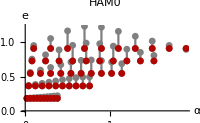
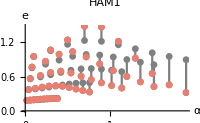
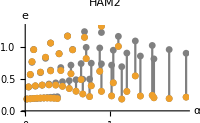
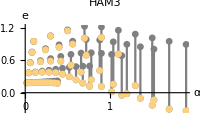
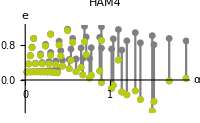
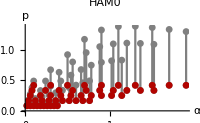
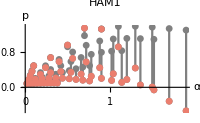
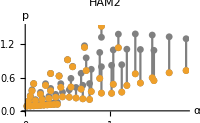

```mathematica
PlotComparison
```

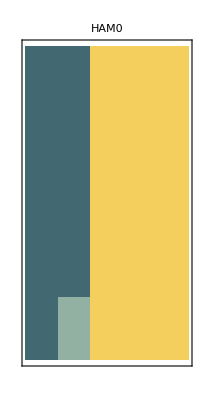
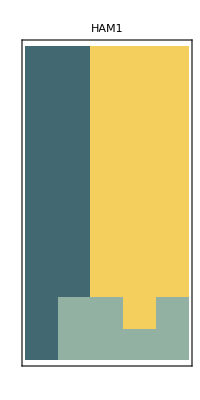
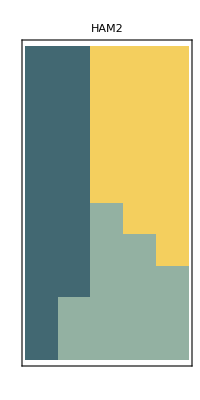
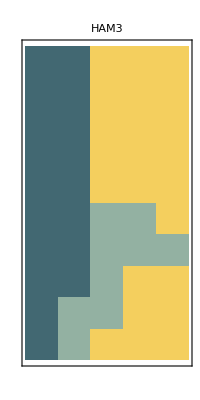
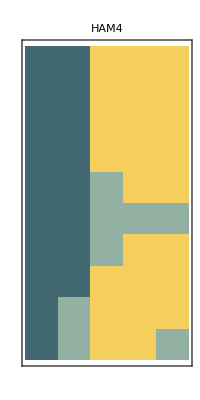
{-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-,}

```mathematica
PlotParadoxical
```

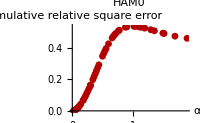
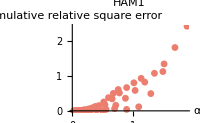
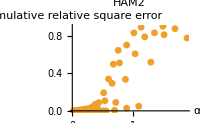
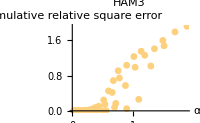
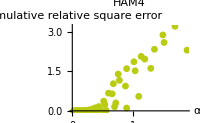

```mathematica
PlotCSError
```

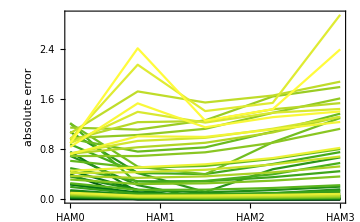

```mathematica
PlotConvergenceCheck
```

## Generalized Newtonian iteration method N(u):-u+Wϕ(u)+h=0

```mathematica
(*start from a given w and h of L2norm 1 and modify their 1norm*)
ψmx=1;
cmx=1;
ψmn=.1;
cmn=.2;
ψst=.1;
cst=.1;
w={{0.54,-0.26},{0.81,-0.11}};
h={0.91,0.42};
Norm[h]
Norm[w]
```

1.00225

1.00232

```mathematica
(*define a generic transfer function, it can be very non linear*)
```

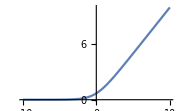

```mathematica
ϕ[x_]:=Log[1+Exp[x]]
Plot[ϕ[x],{x,-10,10},PlotRange->{{-10,10},All},ImageSize->Small]
```

```mathematica
err[{ue_,ui_},W_,H_]:=Total@((-{ue,ui}+W.ϕ[{ue,ui}]+H)^2);
Findc0[u_,W_,H_]:=With[{minsol=Minimize[err[u,W,H],C0]},Part[Values@Last@minsol,1]];
tmax=40;
res=Table[(*define the problem with the current norms ψ and c*)
W=ψ w;
H=c h;
M=Inverse[IdentityMatrix[2]-W];
Df[x_]:=-1+W.D[ϕ[x],x];
D2f[x_]:=W.D[ϕ[x],{x,2}];
(*numerically find solution for the nonlinear problem*)
solD=NDSolve[{ue'[t]==-ue[t]+  W[[1,1]]ϕ[ue[t]]+W[[1,2]]ϕ[ up[t]]+H[[1]],up'[t]==-up[t]+  W[[2,1]] ϕ[ue[t]]+W[[2,2]] ϕ[up[t]]+H[[2]],ue[0]==0.1,up[0]==0.1},{ue[t],up[t]},{t,0,tmax}];
(*find HAM approximate solution with optimal convergence parameter*)
u0=M.H;(*HAM0 contributions*)
U0=u0;(*HAM0 solution*)
auxu1[c0_]:=c0(-(-u0+W.ϕ[u0]+H)(Df[x]/.{x->u0})^-1);(*HAM1 contributions*)
auxU1[c0_]:=u0+auxu1[c0];
c0=Findc0[auxU1[C0],W,H];
u1=auxu1[c0];
U1=auxU1[c0];(*HAM1 solution for the total current*)
u1NOc0=auxu1[1];(*HAM1 contributions*)
auxu2[c0_]:=-1/2 u1^2(D2f[x]/.{x->u0})(Df[x]/.{x->u0})^-1-(c0-1)u1;
auxU2[c0_]:=U1+auxu2[c0];
c0=Findc0[auxU2[C0],W,H];
u2=auxu2[c0];
U2=auxU2[c0];
{Flatten[Evaluate[{ue[t],up[t]}/.solD/.t->tmax]],U0,U1,U2},
{ψ,ψmn,ψmx,ψst},{c,cmn,cmx,cst}];
α=Table[c ψ,{ψ,ψmn,ψmx,ψst},{c,cmn,cmx,cst}];
dd1=Dimensions[α][[1]];
dd2=Dimensions[α][[2]];
ddm=Dimensions[res][[3]];
```

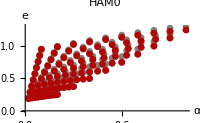
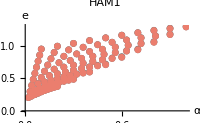
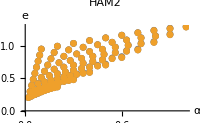
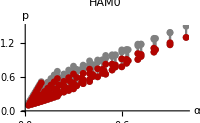
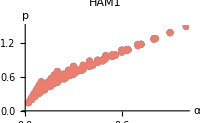
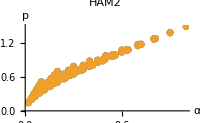

```mathematica
PlotComparison
```

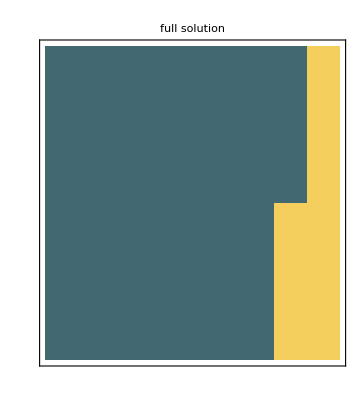
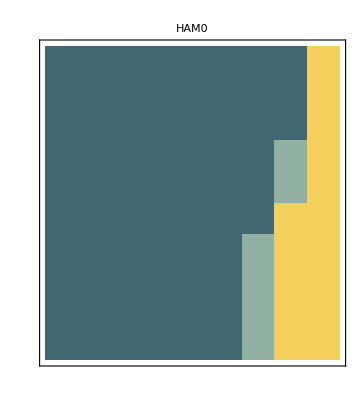
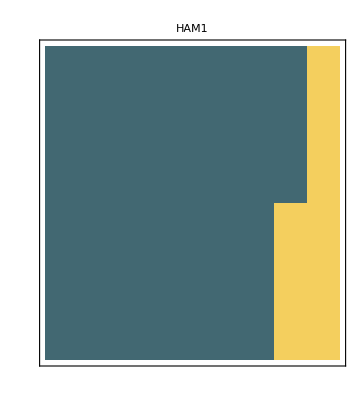
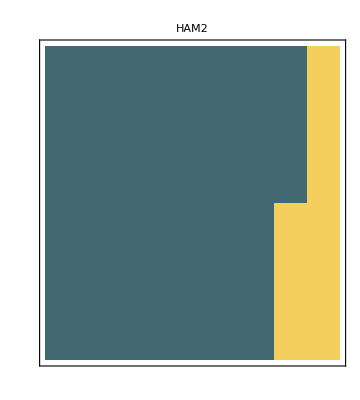

```mathematica
PlotParadoxical
```

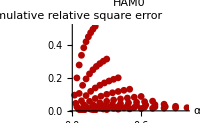
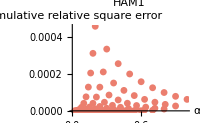
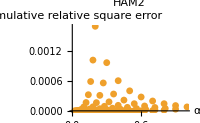

```mathematica
PlotCSError
```

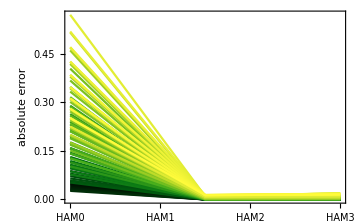

```mathematica
PlotConvergenceCheck
```

## Spatial problem (1 population)

```mathematica
Clear[W,H,U1]
Nn=30;
cent=Nn/2;
σ=(Round[Nn/8])^2;(*this is the variance*)
σr=(Round[Nn/6])^2;
h0=1;
W0=-2;
G[z_,s_]:=1/Sqrt[2π s] Exp[-z^2/(2s)];(*fix normalization because it is discrete*)

solσu=Last@Solve[2 σu^-1==σ^-1+(σr+σu/2)^-1,σu];
σru=σr+σu/2/.solσu;
U1[z_]:=(W0/(2Sqrt[π σru])+h0)G[z-cent,σ];
H=h0 Table[G[z-cent,σ],{z,0,Nn}];
W=W0 Table[G[z-y,σr],{z,0,Nn},{y,0,Nn}];
```

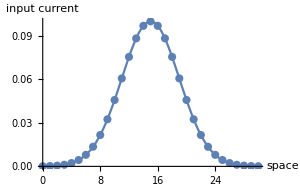
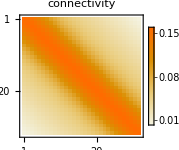

```mathematica
Row[{Show[{ListPlot[H,PlotRange->All,ImageSize->300,DataRange->{0,Nn},AxesLabel->{"space","input current"}],Plot[h0 G[(z-cent),σ],{z,0,30}]}],MatrixPlot[Abs[W],PlotLegends->Automatic,ImageSize->150,PlotLabel->"connectivity"]}]
```

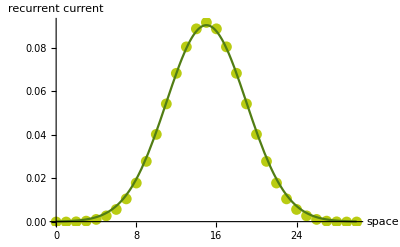

```mathematica
tmax=20;
sol=NDSolveValue[{X'[t]==-X[t]+W.(X[t])^2+H,X[0]==ConstantArray[1.,Nn+1]},X,{t,0,tmax}];
Show[{ListPlot[Evaluate[sol[tmax]],DataRange->{0,Nn},PlotRange->All,AxesLabel->{"space","recurrent current"},PlotLegends->Placed[LineLegend[{"simulat"},LabelStyle->{GrayLevel[0.3],20}],{0.85,0.75}],PlotStyle->ColorData[10]@5],Plot[U1[z],{z,0,30},PlotLegends->Placed[LineLegend[{"HAM1"},LabelStyle->{GrayLevel[0.3],20}],{0.85,0.75}],PlotStyle->ColorData[10]@6]}]
```